Archivos importados correctamente.

ETAPA 1 - STEINHART-HART

A = 0.00112282

B = 0.000235129

C = 8.36684×10^-8

R2 = 0.999997

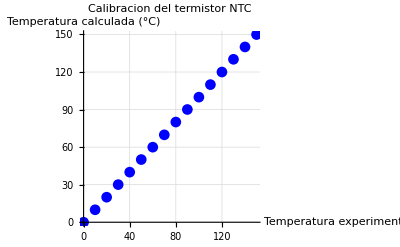

MODELO BETA

Resistencia a 25 °C = 9967.1 ohms

Beta = 3991.88 K

AJUSTES POLINOMIALES RDS(on)

Grado 1: 8.28134+0.0514662 z

R2 = 0.981711

Grado 2: 7.88102+0.0437458 z+0.000132263 z^2

R2 = 0.999749

Grado 3: 7.88242+0.0437134 z+0.000131523 z^2+8.20773×10^-9 z^3

R2 = 0.999749

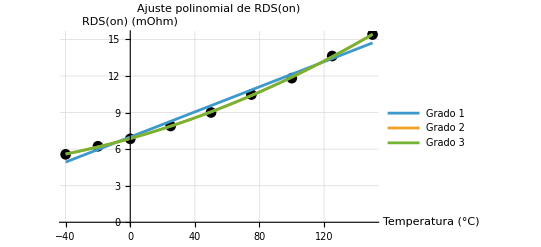

Residuos del polinomio de grado 1

Residuos del polinomio de grado 2

Residuos del polinomio de grado 3

ETAPA 2 - ANALISIS DEL ENFRIAMIENTO

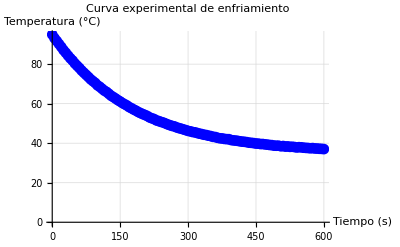

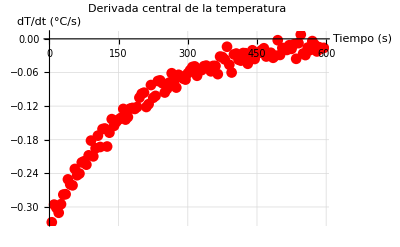

RESULTADOS DE LA ETAPA 2

Temperatura ambiente = 35 °C

Resistencia termica = 3 K/W

Constante de tiempo tau = 179.786 s

Capacitancia termica Ch = 59.9287 J/K

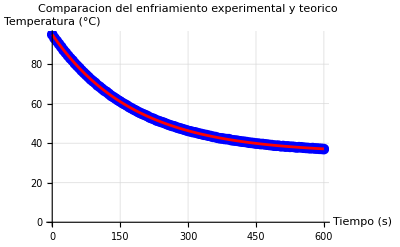

"

```mathematica
(*PROYECTO DE METODOS NUMERICOS*)ClearAll["Global`*"];

(*1. UBICACION E IMPORTACION DE ARCHIVOS*)

SetDirectory[NotebookDirectory[]];

If[!And@@(FileExistsQ/@{"calibracion_ntc.csv","rds_on.csv","enfriamiento.csv"}),Print["ERROR: No se encontraron todos los archivos CSV."];
Print["Archivos encontrados: ",FileNames["*.csv"]];
Abort[];];

rawNTC=Import["calibracion_ntc.csv","CSV"];
rawRDS=Import["rds_on.csv","CSV"];
rawEnfriamiento=Import["enfriamiento.csv","CSV"];

datosNTC=N[Rest[rawNTC]];
datosRDS=N[Rest[rawRDS]];
datosEnfriamiento=N[Rest[rawEnfriamiento]];

Print["Archivos importados correctamente."];


(*ETAPA 1:CALIBRACION DEL TERMISTOR NTC*)

(*Obtener temperaturas y resistencias*)

temperaturasNTC=datosNTC[[All,1]]+273.15;
resistenciasNTC=datosNTC[[All,2]];

(*Ajuste de Steinhart-Hart*)

xNTC=Log[resistenciasNTC];

matrizNTC=Transpose[{ConstantArray[1.,Length[xNTC]],xNTC,xNTC^3}];

coeficientesSH=LeastSquares[matrizNTC,1./temperaturasNTC];

{coefA,coefB,coefC}=coeficientesSH;

temperaturasCalculadas=(1/(coefA+coefB Log[#]+coefC Log[#]^3)-273.15)&/@resistenciasNTC;

r2SH=1-Total[(temperaturasNTC-(temperaturasCalculadas+273.15))^2]/Total[(temperaturasNTC-Mean[temperaturasNTC])^2];

Print[" "];
Print["ETAPA 1 - STEINHART-HART"];
Print["A = ",coefA];
Print["B = ",coefB];
Print["C = ",coefC];
Print["R2 = ",r2SH];

(*Grafica de calibracion NTC*)

ListPlot[Transpose[{datosNTC[[All,1]],temperaturasCalculadas}],PlotStyle->Blue,PlotMarkers->Automatic,AxesLabel->{"Temperatura experimental (°C)","Temperatura calculada (°C)"},PlotLabel->"Calibracion del termistor NTC",GridLines->Automatic]



(*MODELO BETA DEL TERMISTOR*)


xBeta=1./temperaturasNTC-1./298.15;

matrizBeta=Transpose[{ConstantArray[1.,Length[xBeta]],xBeta}];

coeficientesBeta=LeastSquares[matrizBeta,Log[resistenciasNTC]];

lnR25=coeficientesBeta[[1]];
betaNTC=coeficientesBeta[[2]];

Print[" "];
Print["MODELO BETA"];
Print["Resistencia a 25 °C = ",Exp[lnR25]," ohms"];
Print["Beta = ",betaNTC," K"];



(*AJUSTE POLINOMIAL DE RDS(on)*)

temperaturasRDS=datosRDS[[All,1]];
resistenciasRDS=datosRDS[[All,2]];

(*Se centra la temperatura en 25 °C*)

xRDS=temperaturasRDS-25;

datosAjusteRDS=Transpose[{xRDS,resistenciasRDS}];

(*Ajustes de grados 1,2 y 3*)

ajustesRDS=Table[Fit[datosAjusteRDS,Table[z^k,{k,0,grado}],z],{grado,1,3}];

(*Calcular residuos*)

residuosRDS=Table[resistenciasRDS-((ajustesRDS[[grado]]/. z->#)&/@xRDS),{grado,1,3}];

(*Calcular R2*)

r2RDS=Table[1-Total[residuosRDS[[grado]]^2]/Total[(resistenciasRDS-Mean[resistenciasRDS])^2],{grado,1,3}];

Print[" "];
Print["AJUSTES POLINOMIALES RDS(on)"];

Do[Print["Grado ",grado,": ",ajustesRDS[[grado]]];
Print["R2 = ",r2RDS[[grado]]],{grado,1,3}];

(*Grafica de los ajustes*)

Show[ListPlot[Transpose[{temperaturasRDS,resistenciasRDS}],PlotStyle->Black,PlotMarkers->Automatic],Plot[Evaluate[Table[ajustesRDS[[grado]]/. z->(temp-25),{grado,1,3}]],{temp,Min[temperaturasRDS],Max[temperaturasRDS]},PlotLegends->{"Grado 1","Grado 2","Grado 3"}],AxesLabel->{"Temperatura (°C)","RDS(on) (mOhm)"},PlotLabel->"Ajuste polinomial de RDS(on)",GridLines->Automatic]

(*Grafica de residuos*)

Do[Print["Residuos del polinomio de grado ",grado];
ListPlot[Transpose[{temperaturasRDS,residuosRDS[[grado]]}],PlotStyle->Blue,PlotMarkers->Automatic,AxesLabel->{"Temperatura (°C)","Residuo (mOhm)"},PlotLabel->"Residuos del ajuste de grado "<>ToString[grado],GridLines->Automatic],{grado,1,3}];



(*ETAPA 2:ANALISIS DEL ENFRIAMIENTO*)


(*Obtener tiempo y resistencia*)

tiempos=datosEnfriamiento[[All,1]];
resistenciasEnfriamiento=datosEnfriamiento[[All,2]];

(*Convertir resistencia a temperatura usando Steinhart-Hart*)

temperaturasEnfriamiento=(1/(coefA+coefB Log[#]+coefC Log[#]^3)-273.15)&/@resistenciasEnfriamiento;

datosTemperatura=Transpose[{tiempos,temperaturasEnfriamiento}];

Print[" "];
Print["ETAPA 2 - ANALISIS DEL ENFRIAMIENTO"];

(*Grafica de enfriamiento*)

ListPlot[datosTemperatura,PlotStyle->Blue,PlotMarkers->Automatic,AxesLabel->{"Tiempo (s)","Temperatura (°C)"},PlotLabel->"Curva experimental de enfriamiento",GridLines->Automatic]



(*DIFERENCIAS FINITAS*)

derivadaAdelante=Differences[temperaturasEnfriamiento]/Differences[tiempos];

derivadaCentral=Table[(temperaturasEnfriamiento[[i+1]]-temperaturasEnfriamiento[[i-1]])/(tiempos[[i+1]]-tiempos[[i-1]]),{i,2,Length[tiempos]-1}];

derivadaAtras=Differences[temperaturasEnfriamiento]/Differences[tiempos];

datosDerivadaCentral=Transpose[{tiempos[[2;;-2]],derivadaCentral}];

ListPlot[datosDerivadaCentral,PlotStyle->Red,PlotMarkers->Automatic,AxesLabel->{"Tiempo (s)","dT/dt (°C/s)"},PlotLabel->"Derivada central de la temperatura",GridLines->Automatic]



(*AJUSTE EXPONENCIAL Y CALCULO DE Ch*)


temperaturaAmbiente=35;
resistenciaTermica=3;

ajusteEnfriamiento=FindFit[datosTemperatura,temperaturaAmbiente+amplitud Exp[-tiempoModelo/tauModelo],{{amplitud,First[temperaturasEnfriamiento]-temperaturaAmbiente},{tauModelo,180}},tiempoModelo];

amplitudCalculada=amplitud/. ajusteEnfriamiento;
tauCalculada=tauModelo/. ajusteEnfriamiento;

capacitanciaTermica=tauCalculada/resistenciaTermica;

Print[" "];
Print["RESULTADOS DE LA ETAPA 2"];
Print["Temperatura ambiente = ",temperaturaAmbiente," °C"];
Print["Resistencia termica = ",resistenciaTermica," K/W"];
Print["Constante de tiempo tau = ",tauCalculada," s"];
Print["Capacitancia termica Ch = ",capacitanciaTermica," J/K"];



(*COMPARACION DEL MODELO CON LOS DATOS*)

Show[ListPlot[datosTemperatura,PlotStyle->Blue,PlotMarkers->Automatic],Plot[temperaturaAmbiente+amplitudCalculada Exp[-tiempoModelo/tauCalculada],{tiempoModelo,Min[tiempos],Max[tiempos]},PlotStyle->Red],AxesLabel->{"Tiempo (s)","Temperatura (°C)"},PlotLabel->"Comparacion del enfriamiento experimental y teorico",GridLines->Automatic]

Print[" "];
Print["FIN DE LAS ETAPAS 1 Y 2"];
```

ETAPA 3 - MODELO DE UN NODO

RESULTADOS DEL MODELO DE UN NODO

Solucion exacta = 65.0728 °C

Euler = 65.0881 °C

Heun = 65.0728 °C

RK4 = 65.0728 °C

Error Euler = 0.015238

Error Heun = 0.0000183563

Error RK4 = 1.19229×10^-11

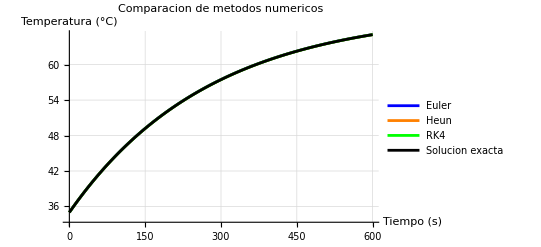

MODELO DE DOS NODOS

RESULTADOS SIN VENTILADOR

Temperatura maxima del MOSFET = 127.366 °C

Temperatura maxima del disipador = 100.377 °C

RESULTADOS CON VENTILADOR

Temperatura maxima del MOSFET = 81.317 °C

Temperatura maxima del disipador = 60.0124 °C

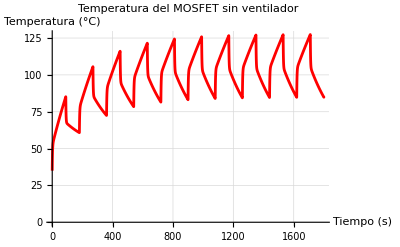

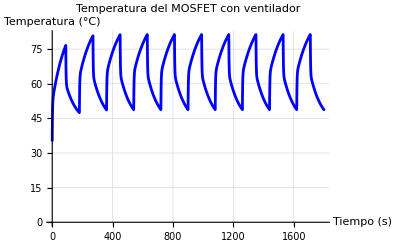

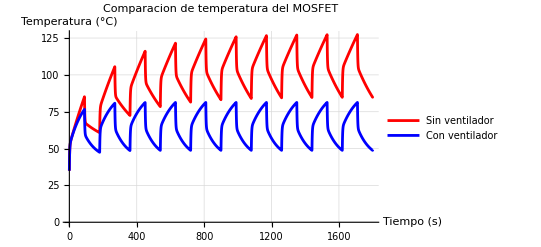

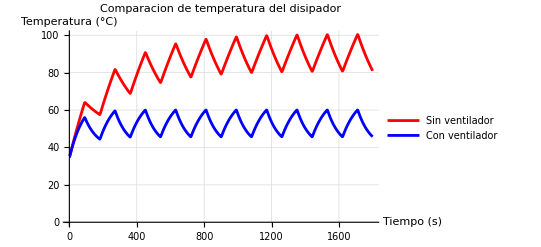

FIN DE LA ETAPA 3

```mathematica
(*ETAPA 3:SIMULACION TERMICA DEL MOSFET*)
(*MODELO DE UN NODO*)
Print["ETAPA 3 - MODELO DE UN NODO"];

(*Parametros*)

capacidad=62.;
resistencia=3.8;
corriente=30.;
resistencia25=0.008;
alfa=0.0055;
ambiente=35.;
temperaturaInicial=35.;

tiempoFinal=600.;
paso=1.;

(*Ecuacion diferencial*)

fUnNodo[t_,temp_]:=(corriente^2*resistencia25*(1+alfa*(temp-25))-(temp-ambiente)/resistencia)/capacidad;

(*Solucion exacta*)

q1=(corriente^2*resistencia25*alfa-1/resistencia)/capacidad;

q0=(corriente^2*resistencia25*(1-alfa*25)+ambiente/resistencia)/capacidad;

temperaturaEstacionaria=-q0/q1;

temperaturaExacta[t_]:=temperaturaEstacionaria+(temperaturaInicial-temperaturaEstacionaria)*Exp[q1*t];

(*Funcion para un paso de Euler*)

pasoEuler[f_,t_,y_,h_]:=y+h*f[t,y];

(*Funcion para un paso de Heun*)

pasoHeun[f_,t_,y_,h_]:=Module[{k1,k2},k1=f[t,y];
k2=f[t+h,y+h*k1];
y+h*(k1+k2)/2];

(*Funcion para un paso de Runge-Kutta 4*)

pasoRK4[f_,t_,y_,h_]:=Module[{k1,k2,k3,k4},k1=f[t,y];
k2=f[t+h/2,y+h*k1/2];
k3=f[t+h/2,y+h*k2/2];
k4=f[t+h,y+h*k3];
y+h*(k1+2*k2+2*k3+k4)/6];

(*Simulacion de Euler*)

simularEuler[f_,y0_,tf_,h_]:=Module[{n,t=0.,y=y0,resultados,i},n=Round[tf/h];
resultados={{0.,y0}};
Do[y=pasoEuler[f,t,y,h];
t=i*h;
AppendTo[resultados,{t,y}],{i,1,n}];
resultados];

(*Simulacion de Heun*)

simularHeun[f_,y0_,tf_,h_]:=Module[{n,t=0.,y=y0,resultados,i},n=Round[tf/h];
resultados={{0.,y0}};
Do[y=pasoHeun[f,t,y,h];
t=i*h;
AppendTo[resultados,{t,y}],{i,1,n}];
resultados];

(*Simulacion de RK4*)

simularRK4[f_,y0_,tf_,h_]:=Module[{n,t=0.,y=y0,resultados,i},n=Round[tf/h];
resultados={{0.,y0}};
Do[y=pasoRK4[f,t,y,h];
t=i*h;
AppendTo[resultados,{t,y}],{i,1,n}];
resultados];

(*Ejecutar los tres metodos*)

resultadoEuler=simularEuler[fUnNodo,temperaturaInicial,tiempoFinal,paso];

resultadoHeun=simularHeun[fUnNodo,temperaturaInicial,tiempoFinal,paso];

resultadoRK4=simularRK4[fUnNodo,temperaturaInicial,tiempoFinal,paso];

(*Comparar con la solucion exacta*)

temperaturaFinalExacta=temperaturaExacta[tiempoFinal];

temperaturaFinalEuler=Last[resultadoEuler][[2]];
temperaturaFinalHeun=Last[resultadoHeun][[2]];
temperaturaFinalRK4=Last[resultadoRK4][[2]];

Print[" "];
Print["RESULTADOS DEL MODELO DE UN NODO"];

Print["Solucion exacta = ",temperaturaFinalExacta," °C"];
Print["Euler = ",temperaturaFinalEuler," °C"];
Print["Heun = ",temperaturaFinalHeun," °C"];
Print["RK4 = ",temperaturaFinalRK4," °C"];

Print["Error Euler = ",Abs[temperaturaFinalEuler-temperaturaFinalExacta]];

Print["Error Heun = ",Abs[temperaturaFinalHeun-temperaturaFinalExacta]];

Print["Error RK4 = ",Abs[temperaturaFinalRK4-temperaturaFinalExacta]];

(*Grafica comparativa*)

ListLinePlot[{resultadoEuler,resultadoHeun,resultadoRK4,Table[{t,temperaturaExacta[t]},{t,0,tiempoFinal,1}]},PlotLegends->{"Euler","Heun","RK4","Solucion exacta"},PlotStyle->{Blue,Orange,Green,Black},AxesLabel->{"Tiempo (s)","Temperatura (°C)"},PlotLabel->"Comparacion de metodos numericos",GridLines->Automatic]



(*2. MODELO DE DOS NODOS*)

Print[" "];
Print["MODELO DE DOS NODOS"];

(*Parametros termicos*)

Cj=2.;
Ch=capacitanciaTermica;

Rjh=0.8;
RhaSinVentilador=3.;
RhaConVentilador=1.2;

Ta=35.;

temperaturaInicialJ=35.;
temperaturaInicialH=35.;

tiempoSimulacion=1800.;
pasoDosNodos=0.25;

(*Corriente:50 A durante 90 s y 20 A durante 90 s*)

corrienteDosNodos[t_]:=If[Mod[t,180]<90,50.,20.];

(*Resistencia del MOSFET usando el polinomio de grado 2*)

rdsOhm[temp_]:=0.001*(ajustesRDS[[2]]/. z->(temp-25));

(*Ecuaciones diferenciales de dos nodos*)

fDosNodos[ra_][t_,estado_]:=Module[{tj,th,potencia,dTj,dTh},tj=estado[[1]];
th=estado[[2]];
potencia=corrienteDosNodos[t]^2*rdsOhm[tj];
dTj=(potencia-(tj-th)/Rjh)/Cj;
dTh=((tj-th)/Rjh-(th-Ta)/ra)/Ch;
{dTj,dTh}];

(*Condiciones iniciales*)

condicionesIniciales={temperaturaInicialJ,temperaturaInicialH};

(*Simulacion sin ventilador*)

resultadoSinVentilador=simularRK4[fDosNodos[RhaSinVentilador],condicionesIniciales,tiempoSimulacion,pasoDosNodos];

(*Simulacion con ventilador*)

resultadoConVentilador=simularRK4[fDosNodos[RhaConVentilador],condicionesIniciales,tiempoSimulacion,pasoDosNodos];

(*Obtener temperaturas*)

temperaturaJSin=resultadoSinVentilador[[All,2,1]];

temperaturaHSin=resultadoSinVentilador[[All,2,2]];

temperaturaJCon=resultadoConVentilador[[All,2,1]];

temperaturaHCon=resultadoConVentilador[[All,2,2]];

(*Temperaturas maximas*)

maximoJSin=Max[temperaturaJSin];
maximoHSin=Max[temperaturaHSin];

maximoJCon=Max[temperaturaJCon];
maximoHCon=Max[temperaturaHCon];

Print[" "];
Print["RESULTADOS SIN VENTILADOR"];

Print["Temperatura maxima del MOSFET = ",maximoJSin," °C"];

Print["Temperatura maxima del disipador = ",maximoHSin," °C"];

Print[" "];
Print["RESULTADOS CON VENTILADOR"];

Print["Temperatura maxima del MOSFET = ",maximoJCon," °C"];

Print["Temperatura maxima del disipador = ",maximoHCon," °C"];



(*GRAFICAS DEL MODELO DE DOS NODOS*)


(*MOSFET sin ventilador*)

ListLinePlot[Transpose[{resultadoSinVentilador[[All,1]],temperaturaJSin}],PlotStyle->Red,AxesLabel->{"Tiempo (s)","Temperatura (°C)"},PlotLabel->"Temperatura del MOSFET sin ventilador",GridLines->Automatic]

(*MOSFET con ventilador*)

ListLinePlot[Transpose[{resultadoConVentilador[[All,1]],temperaturaJCon}],PlotStyle->Blue,AxesLabel->{"Tiempo (s)","Temperatura (°C)"},PlotLabel->"Temperatura del MOSFET con ventilador",GridLines->Automatic]

(*Comparacion de temperaturas del MOSFET*)

ListLinePlot[{Transpose[{resultadoSinVentilador[[All,1]],temperaturaJSin}],Transpose[{resultadoConVentilador[[All,1]],temperaturaJCon}]},PlotLegends->{"Sin ventilador","Con ventilador"},PlotStyle->{Red,Blue},AxesLabel->{"Tiempo (s)","Temperatura (°C)"},PlotLabel->"Comparacion de temperatura del MOSFET",GridLines->Automatic]

(*Comparacion de temperaturas del disipador*)

ListLinePlot[{Transpose[{resultadoSinVentilador[[All,1]],temperaturaHSin}],Transpose[{resultadoConVentilador[[All,1]],temperaturaHCon}]},PlotLegends->{"Sin ventilador","Con ventilador"},PlotStyle->{Red,Blue},AxesLabel->{"Tiempo (s)","Temperatura (°C)"},PlotLabel->"Comparacion de temperatura del disipador",GridLines->Automatic]

Print[" "];
Print["FIN DE LA ETAPA 3"];
```

ETAPA 4: ENERGIA Y MONTE CARLO

TABLA DE ENERGIA Y POTENCIA MEDIA

Paso (s) | Condicion | Energia Trapecio (J) | Potencia media Trapecio (W) | Energia Simpson (J) | Potencia media Simpson (W)
1 | Sin ventilador | 31769.8 | 17.6499 | 31779.3 | 17.6552
1 | Con ventilador | 26486.7 | 14.7148 | 26493.5 | 14.7186
5 | Sin ventilador | 31646. | 17.5811 | 31704.8 | 17.6138
5 | Con ventilador | 26398.1 | 14.6656 | 26440.6 | 14.6892
10 | Sin ventilador | 31469.5 | 17.4831 | 30695.4 | 17.053
10 | Con ventilador | 26270.6 | 14.5948 | 25623.8 | 14.2355

ENERGIA DE REFERENCIA

Sin ventilador = 31790. J

Con ventilador = 26501. J

ERRORES DE MONTE CARLO

N | Error sin ventilador (J) | Error con ventilador (J)
100 | 3150.42 | 2909.59
1000 | 577.266 | 736.95
10000 | 269.316 | 197.729
100000 | 71.3316 | 66.0468
1000000 | 20.6706 | 24.3656

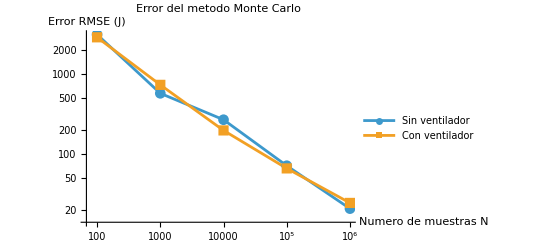

PROBABILIDAD DE FALLA

RESULTADOS DE PROBABILIDAD DE FALLA

SIN VENTILADOR

Fallas = 522

Probabilidad = 52.2 %

Intervalo de confianza = 49.104 % a 55.296 %

CON VENTILADOR

Fallas = 0

Probabilidad = 0. %

Intervalo de confianza = 0. % a 0. %

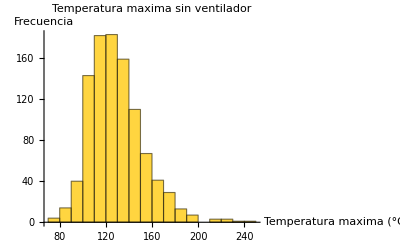

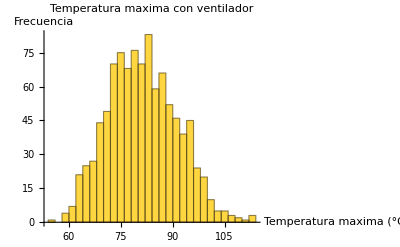

FIN DE LA ETAPA 4

```mathematica
(*ETAPA 4:ENERGIA Y SIMULACION MONTE CARLO*)
Print["ETAPA 4: ENERGIA Y MONTE CARLO"];


(*1. CALCULO DE POTENCIA Y ENERGIA*)


tiempoTotal=1800.;
pasoBase=pasoDosNodos;

(*Calcular potencia instantanea*)

potenciaSin=Table[corrienteDosNodos[resultadoSinVentilador[[i,1]]]^2*rdsOhm[resultadoSinVentilador[[i,2,1]]],{i,1,Length[resultadoSinVentilador]}];

	qpotenciaCon=Table[corrienteDosNodos[resultadoConVentilador[[i,1]]]^2*rdsOhm[resultadoConVentilador[[i,2,1]]],{i,1,Length[resultadoConVentilador]}];

(*Crear datos de potencia para cada intervalo*)

crearDatosPotencia[resultado_,h_]:=Module[{salto,posiciones,tiemposMuestra,potenciasMuestra},salto=Round[h/pasoBase];
posiciones=Range[1,Length[resultado],salto];
tiemposMuestra=resultado[[posiciones,1]];
potenciasMuestra=Table[corrienteDosNodos[tiemposMuestra[[i]]]^2*rdsOhm[resultado[[posiciones[[i]],2,1]]],{i,1,Length[posiciones]}];
Transpose[{tiemposMuestra,potenciasMuestra}]];

(*Regla del trapecio*)

reglaTrapecio[valores_,h_]:=h*((First[valores]+Last[valores])/2+Total[Rest[Most[valores]]]);

(*Regla de Simpson 1/3*)

reglaSimpson[valores_,h_]:=Module[{n=Length[valores]-1},If[OddQ[n],Return[$Failed]];
h/3*(First[valores]+Last[valores]+4*Total[valores[[2;;-2;;2]]]+2*Total[valores[[3;;-2;;2]]])];

(*Calcular energia para cada intervalo*)

intervalos={1,5,10};

resultadosEnergia={};

Do[datosSin=crearDatosPotencia[resultadoSinVentilador,h];
datosCon=crearDatosPotencia[resultadoConVentilador,h];
valoresSin=datosSin[[All,2]];
valoresCon=datosCon[[All,2]];
(*Energia sin ventilador*)energiaTrapSin=reglaTrapecio[valoresSin,h];
energiaSimpSin=reglaSimpson[valoresSin,h];
(*Energia con ventilador*)energiaTrapCon=reglaTrapecio[valoresCon,h];
energiaSimpCon=reglaSimpson[valoresCon,h];
AppendTo[resultadosEnergia,{h,"Sin ventilador",energiaTrapSin,energiaTrapSin/tiempoTotal,energiaSimpSin,energiaSimpSin/tiempoTotal}];
AppendTo[resultadosEnergia,{h,"Con ventilador",energiaTrapCon,energiaTrapCon/tiempoTotal,energiaSimpCon,energiaSimpCon/tiempoTotal}],{h,intervalos}];

Print[" "];
Print["TABLA DE ENERGIA Y POTENCIA MEDIA"];

Print[TableForm[resultadosEnergia,TableHeadings->{None,{"Paso (s)","Condicion","Energia Trapecio (J)","Potencia media Trapecio (W)","Energia Simpson (J)","Potencia media Simpson (W)"}}]];



(*2. ENERGIA DE REFERENCIA*)


energiaReferenciaSin=reglaTrapecio[potenciaSin,pasoBase];

energiaReferenciaCon=reglaTrapecio[potenciaCon,pasoBase];

Print[" "];
Print["ENERGIA DE REFERENCIA"];

Print["Sin ventilador = ",energiaReferenciaSin," J"];

Print["Con ventilador = ",energiaReferenciaCon," J"];



(*3. METODO MONTE CARLO PARA ENERGIA*)


(*Interpolacion de la potencia*)

tiemposFinos=resultadoSinVentilador[[All,1]];

funcionPotenciaSin=Interpolation[Transpose[{tiemposFinos,potenciaSin}],InterpolationOrder->1];

funcionPotenciaCon=Interpolation[Transpose[{tiemposFinos,potenciaCon}],InterpolationOrder->1];

(*Cantidades de muestras*)

cantidadesN={100,1000,10000,100000,1000000};

repeticiones=10;

(*Funcion Monte Carlo*)

monteCarloEnergia[funcion_,n_]:=tiempoTotal*Mean[funcion/@RandomReal[{0,tiempoTotal},n]];

(*Repetir los calculos*)

SeedRandom[1234];

resultadosMCSin=Table[Table[monteCarloEnergia[funcionPotenciaSin,n],{repeticiones}],{n,cantidadesN}];

resultadosMCCon=Table[Table[monteCarloEnergia[funcionPotenciaCon,n],{repeticiones}],{n,cantidadesN}];

(*Calcular error RMSE*)

errorMCSin=Table[Sqrt[Mean[(resultadosMCSin[[i]]-energiaReferenciaSin)^2]],{i,1,Length[cantidadesN]}];

errorMCCon=Table[Sqrt[Mean[(resultadosMCCon[[i]]-energiaReferenciaCon)^2]],{i,1,Length[cantidadesN]}];

Print[" "];
Print["ERRORES DE MONTE CARLO"];

Print[TableForm[Transpose[{cantidadesN,errorMCSin,errorMCCon}],TableHeadings->{None,{"N","Error sin ventilador (J)","Error con ventilador (J)"}}]];

(*Grafica de error*)

ListLogLogPlot[{Transpose[{cantidadesN,errorMCSin}],Transpose[{cantidadesN,errorMCCon}]},Joined->True,PlotMarkers->Automatic,PlotLegends->{"Sin ventilador","Con ventilador"},AxesLabel->{"Numero de muestras N","Error RMSE (J)"},PlotLabel->"Error del metodo Monte Carlo",GridLines->Automatic]



(*4. PROBABILIDAD DE FALLA*)

Print[" "];
Print["PROBABILIDAD DE FALLA"];

(*Funcion para una simulacion con parametros variables*)

simulacionFalla[ra_,ch_,ta_,r25_,h_]:=Module[{y,t,f,maximo,n},y={ta,ta};
t=0.;
maximo=ta;
n=Round[tiempoTotal/h];
f=Function[{tt,estado},Module[{tj,th,potencia,dTj,dTh},tj=estado[[1]];
th=estado[[2]];
potencia=corrienteDosNodos[tt]^2*rdsOhm[tj]*(r25/8.);
dTj=(potencia-(tj-th)/Rjh)/Cj;
dTh=((tj-th)/Rjh-(th-ta)/ra)/ch;
{dTj,dTh}]];
Do[y=pasoRK4[f,t,y,h];
t=i*h;
maximo=Max[maximo,y[[1]]],{i,1,n}];
maximo];

(*Numero de simulaciones*)

numeroSimulaciones=1000;

pasoMonteCarlo=2.5;

(*Funcion para generar parametros aleatorios positivos*)

muestraPositiva[distribucion_]:=Module[{valor},valor=RandomVariate[distribucion];
While[valor<=0,valor=RandomVariate[distribucion]];
valor];

(*Simulaciones sin ventilador*)

SeedRandom[2026];

maximosSin=Table[Module[{ra,ch,ta,r25},ra=muestraPositiva[NormalDistribution[3.,0.3]];
ch=muestraPositiva[NormalDistribution[60.,6.]];
ta=RandomReal[{25.,45.}];
r25=muestraPositiva[NormalDistribution[8.,0.8]];
simulacionFalla[ra,ch,ta,r25,pasoMonteCarlo]],{numeroSimulaciones}];

(*Simulaciones con ventilador*)

maximosCon=Table[Module[{ra,ch,ta,r25},ra=muestraPositiva[NormalDistribution[1.2,0.12]];
ch=muestraPositiva[NormalDistribution[60.,6.]];
ta=RandomReal[{25.,45.}];
r25=muestraPositiva[NormalDistribution[8.,0.8]];
simulacionFalla[ra,ch,ta,r25,pasoMonteCarlo]],{numeroSimulaciones}];

(*Determinar fallas*)

fallasSin=Count[maximosSin,x_/;x>125.];

fallasCon=Count[maximosCon,x_/;x>125.];

probabilidadSin=N[fallasSin/numeroSimulaciones];

probabilidadCon=N[fallasCon/numeroSimulaciones];

(*Intervalos de confianza del 95 %*)

intervaloConfianza[p_,n_]:=Module[{error},error=1.96*Sqrt[p*(1-p)/n];
{Max[0.,p-error],Min[1.,p+error]}];

icSin=intervaloConfianza[probabilidadSin,numeroSimulaciones];

icCon=intervaloConfianza[probabilidadCon,numeroSimulaciones];

Print[" "];
Print["RESULTADOS DE PROBABILIDAD DE FALLA"];

Print["SIN VENTILADOR"];
Print["Fallas = ",fallasSin];
Print["Probabilidad = ",100*probabilidadSin," %"];
Print["Intervalo de confianza = ",100*icSin[[1]]," % a ",100*icSin[[2]]," %"];

Print[" "];
Print["CON VENTILADOR"];
Print["Fallas = ",fallasCon];
Print["Probabilidad = ",100*probabilidadCon," %"];
Print["Intervalo de confianza = ",100*icCon[[1]]," % a ",100*icCon[[2]]," %"];



(*5. HISTOGRAMAS DE TEMPERATURA MAXIMA*)


Histogram[maximosSin,20,AxesLabel->{"Temperatura maxima (°C)","Frecuencia"},PlotLabel->"Temperatura maxima sin ventilador"]

Histogram[maximosCon,20,AxesLabel->{"Temperatura maxima (°C)","Frecuencia"},PlotLabel->"Temperatura maxima con ventilador"]

Print[" "];
Print["FIN DE LA ETAPA 4"];
```

```mathematica
(*CORRECCION DE INTEGRACION DE ENERGIA*)(*Separamos los intervalos donde cambia la corriente, Funcion de Simpson 1/3. Si hay un numero impar de subintervalos,usamos Simpson en los primeros y trapecio al final.*)simpsonCorregido[valores_,h_]:=Module[{n,resultado,primeros},n=Length[valores]-1;
If[n<1,Return[0.]];
If[EvenQ[n],Return[h/3*(First[valores]+Last[valores]+4 Total[valores[[2;;-2;;2]]]+2 Total[valores[[3;;-2;;2]]])]];
primeros=Take[valores,n];
resultado=If[n>1,h/3*(First[primeros]+Last[primeros]+4 Total[primeros[[2;;-2;;2]]]+2 Total[primeros[[3;;-2;;2]]]),0.];
resultado+h*(valores[[-2]]+valores[[-1]])/2];

(*Funcion para integrar respetando los cambios de corriente*)

integrarEnergia[resultado_,h_]:=Module[{temperaturaMOSFET,energiaTrap=0.,energiaSimp=0.,inicio,fin,corrienteTramo,tiemposTramo,potenciasTramo,j,energiaLocalTrap,energiaLocalSimp},temperaturaMOSFET=Interpolation[({#[[1]],#[[2,1]]}&)/@resultado,InterpolationOrder->1];
Do[inicio=90.*j;
fin=90.*(j+1);
(*Corriente constante dentro de cada tramo*)corrienteTramo=If[EvenQ[j],50.,20.];
tiemposTramo=Range[inicio,fin,h];
potenciasTramo=(corrienteTramo^2*rdsOhm[temperaturaMOSFET[#]])&/@tiemposTramo;
energiaLocalTrap=reglaTrapecio[potenciasTramo,h];
energiaLocalSimp=simpsonCorregido[potenciasTramo,h];
energiaTrap+=energiaLocalTrap;
energiaSimp+=energiaLocalSimp,{j,0,19}];
{energiaTrap,energiaSimp}];

(*Recalcular para cada intervalo*)

tablaEnergiaCorregida={};

Do[energiaSinCorregida=integrarEnergia[resultadoSinVentilador,h];
energiaConCorregida=integrarEnergia[resultadoConVentilador,h];
AppendTo[tablaEnergiaCorregida,{h,"Sin ventilador",energiaSinCorregida[[1]],energiaSinCorregida[[1]]/1800.,energiaSinCorregida[[2]],energiaSinCorregida[[2]]/1800.}];
AppendTo[tablaEnergiaCorregida,{h,"Con ventilador",energiaConCorregida[[1]],energiaConCorregida[[1]]/1800.,energiaConCorregida[[2]],energiaConCorregida[[2]]/1800.}],{h,{1.,5.,10.}}];

Print["TABLA DE ENERGIA CORREGIDA"];

Print[TableForm[tablaEnergiaCorregida,TableHeadings->{None,{"Paso (s)","Condicion","Energia Trapecio (J)","Potencia media Trapecio (W)","Energia Simpson (J)","Potencia media Simpson (W)"}}]];
```

TABLA DE ENERGIA CORREGIDA

Paso (s) | Condicion | Energia Trapecio (J) | Potencia media Trapecio (W) | Energia Simpson (J) | Potencia media Simpson (W)
1. | Sin ventilador | 31795.1 | 17.664 | 31796.2 | 17.6646
1. | Con ventilador | 26504.6 | 14.7248 | 26505.4 | 14.7252
5. | Sin ventilador | 31772.7 | 17.6515 | 31789.3 | 17.6607
5. | Con ventilador | 26487.3 | 14.7152 | 26500.1 | 14.7223
10. | Sin ventilador | 31722.8 | 17.6238 | 31758.8 | 17.6438
10. | Con ventilador | 26449. | 14.6939 | 26477.1 | 14.7095